## Preliminaries

```mathematica
ClearAll[proof];
proof[v_]/;BooleanQ[v]:=(If[v,
Print[Style["QED■",StandardGreen,Bold,18]],
Print[Style["FAILED PROOF■",StandardRed,Bold,18]]];v);
proof[___]:=Print[Style["INVALID INPUT TO PROOF■",StandardYellow,Bold,18]];
```

## Lie Ontology

### Object Inventory

```mathematica
Module[{data,header,row},
row[col1_,col2_,col3_]:={col1,col2,col3};
header={Style["Short Name",14,Bold],
Style["Item Description",14,Bold],
Style["Context / Physical Interpretation",14,Bold]};
data={header,
row[Subscript["𝔤",""],"Abstract 𝔰𝔲(2)","Abstract Lie algebra: [E_i, E_j] = ϵ_ijk E_k (no sum)"],
row[Subscript["su(2)",2],"𝔰𝔲(2) 2x2 Rep","Complex matrix realization (Generators T_k)"],
row[Subscript["so(3)",3],"𝔰𝔬(3) 3x3 Rep","Real matrix realization (Generators J_k)"],
row["SU(2)","SU(2) Group","2 × 2 unitary matrices, det=1"],
row["SO(3)","SO(3) Group","3 × 3 orthogonal matrices, det=1"],
row["V_spin","Spinors (ℂ^2)","Space for Fundamental Action of SU(2)"],
row["ℝ^3","Real ℝ^3","Euclidean space of physical 3-vectors"],
row["𝔥_0","Mat-Vecs (𝔥_0)","Traceless Hermitian 2 × 2 matrices"],
row["σ_k","Pauli Matrix","Basis {σ_1, σ_2, σ_3} for the Pauli Map"],
row["f_ijk","Structure Constants","Numbers ϵ_ijk characterizing the bracket"],
row["𝒵","Center","The kernel {I, -I} of the SU(2) → SO(3) map"],
row["S^3","Topology S^3","Topology of SU(2) (3-sphere)"],
row["ℝP^3","Topolog ℝP^3","Topology of SO(3) (Projective space)"],
row["ad_X","Infitesimal adjoint","Algebra action [X, ·]"],
row["Ad_Q","Finite Adjoint","Group action Q·Z·Q†"],
row["B","Killing Form","Trace inner product for coordinate extraction"]};
Grid[data,
Alignment->{Left,Baseline},(*Spacings->{2,1.25},*)
Dividers->{None,{1->Directive[White,Thickness[2]],2->White,-1->White}},
Background->{None,{GrayLevel[0.2],{GrayLevel[0.15],GrayLevel[0.12]}}},
ItemStyle->{White,12,FontFamily->"Times"},
ItemSize->{{10,10,25},Automatic}]]
```

Short Name | Item Description | Context / Physical Interpretation
𝔤_ | Abstract 𝔰𝔲(2) | Abstract Lie algebra: [E_i, E_j] = ϵ_ijk E_k (no sum)
(su(2))_2 | 𝔰𝔲(2) 2x2 Rep | Complex matrix realization (Generators T_k)
(so(3))_3 | 𝔰𝔬(3) 3x3 Rep | Real matrix realization (Generators J_k)
SU(2) | SU(2) Group | 2 × 2 unitary matrices, det=1
SO(3) | SO(3) Group | 3 × 3 orthogonal matrices, det=1
V_spin | Spinors (ℂ^2) | Space for Fundamental Action of SU(2)
ℝ^3 | Real ℝ^3 | Euclidean space of physical 3-vectors
𝔥_0 | Mat-Vecs (𝔥_0) | Traceless Hermitian 2 × 2 matrices
σ_k | Pauli Matrix | Basis {σ_1, σ_2, σ_3} for the Pauli Map
f_ijk | Structure Constants | Numbers ϵ_ijk characterizing the bracket
𝒵 | Center | The kernel {I, -I} of the SU(2) → SO(3) map
S^3 | Topology S^3 | Topology of SU(2) (3-sphere)
ℝP^3 | Topolog ℝP^3 | Topology of SO(3) (Projective space)
ad_X | Infitesimal adjoint | Algebra action [X, ·]
Ad_Q | Finite Adjoint | Group action Q·Z·Q†
B | Killing Form | Trace inner product for coordinate extraction

### Mapping Inventory

```mathematica
Module[{data,header,row},(*Helper to keep the data structure clean*)row[src_,target_,mech_,type_]:={src,target,mech,type};
header=Style[#,14,Bold]&/@{"Source","Target","Name / Mechanism","Type"};
data={header,
row[Subscript["su(2)",2],"SU(2)","MatrixExp","Surj"],
row[Subscript["so(3)",3],"SO(3)","MatrixExp","Surj"],
row["SU(2)","SO(3)","Ad Rep / 2-to-1 Cover","Surj (2:1)"],
row["𝒵","SU(2)","Center inclusion","Inj"],
row[Superscript["𝕣",3],Subscript["𝔥",0],"Pauli Map (v · σ)","Bij"],
row[Subscript["𝔥",0],Superscript["𝕣",3],"Trace Projection (getTCoeffs)","Bij"],
row[Subscript["su(2)",2],Subscript["so(3)",3],"Algebra Ad Rep (TtoJ)","Bij"],
row["𝔤",Subscript["f","ijk"],"Basis Mapping","Surj"],
row["SU(2)",Superscript["S",3],"Topo ID","Bij (Diffeo)"],
row["SO(3)",Superscript["RP",3],"Topo ID","Bij (Diffeo)"],
row["SU(2)",Subscript["V","spin"],"Fund Act (Q ψ)","Act"],
row["SU(2)",Subscript["𝔥",0],"Ad Act (Q Z Q†)","Act"],
row["SO(3)",Superscript["𝕣",3],"Standard Rot (R v)","Act"]};
Grid[data,
Alignment->{Left,Baseline},
(*Spacings->{2,1.5},*)
Dividers->{None,{
1->Directive[White,Thickness[2]],
2->White,
7->Directive[White,Thickness[0.5],Opacity[0.3]],
12->Directive[White,Thickness[0.5],Opacity[0.3]],-1->White}},
Background->{None,{GrayLevel[0.2],{GrayLevel[0.15],GrayLevel[0.12]}}},
ItemStyle->{White,12,FontFamily->"Times"},
ItemSize->{{5,5,15,7},Automatic}]]
```

Source | Target | Name / Mechanism | Type
(su(2))_2 | SU(2) | MatrixExp | Surj
(so(3))_3 | SO(3) | MatrixExp | Surj
SU(2) | SO(3) | Ad Rep / 2-to-1 Cover | Surj (2:1)
𝒵 | SU(2) | Center inclusion | Inj
𝕣^3 | 𝔥_0 | Pauli Map (v · σ) | Bij
𝔥_0 | 𝕣^3 | Trace Projection (getTCoeffs) | Bij
(su(2))_2 | (so(3))_3 | Algebra Ad Rep (TtoJ) | Bij
𝔤 | f_ijk | Basis Mapping | Surj
SU(2) | S^3 | Topo ID | Bij (Diffeo)
SO(3) | RP^3 | Topo ID | Bij (Diffeo)
SU(2) | V_spin | Fund Act (Q ψ) | Act
SU(2) | 𝔥_0 | Ad Act (Q Z Q†) | Act
SO(3) | 𝕣^3 | Standard Rot (R v) | Act

### Ontology Diagram

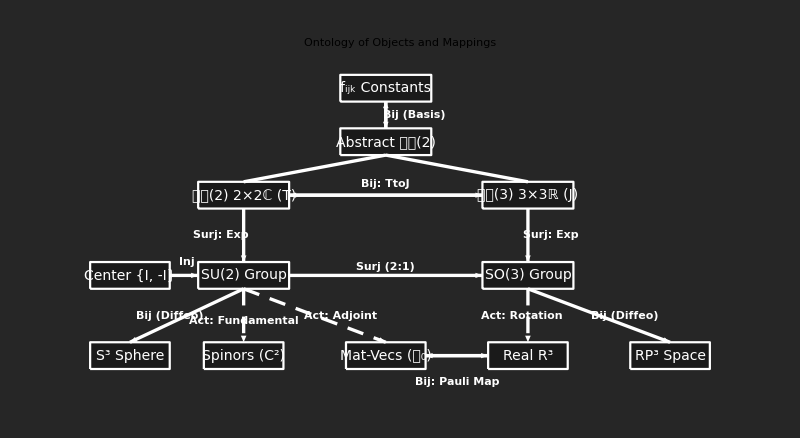

```mathematica
Module[{node, lbl},
 (* Helper functions for consistent styling *)
 node[pos_, txt_, color_: GrayLevel[0.1], w_: 0.8] := {
   EdgeForm[{White, Thickness[0.002]}], color, 
   Rectangle[pos - {w, 0.25}, pos + {w, 0.25}, RoundingRadius -> 0.1], 
   White, Text[Style[txt, 14], pos]
  };
 
 lbl[pos_, txt_] := {
   Text[Style[txt, 11, Bold, Background -> GrayLevel[0.15]], pos]
  };

 Graphics[{
   node[{0, 5}, "f_ijk Constants"], 
   node[{0, 4}, "Abstract 𝔰𝔲(2)"], 
   node[{-2.5, 3}, "𝔰𝔲(2) 2×2ℂ (T)"], 
   node[{2.5, 3}, "𝔰𝔬(3) 3×3ℝ (J)"], 
   node[{-4.5, 1.5}, "Center {I, -I}", GrayLevel[0.1], 0.7], 
   node[{-2.5, 1.5}, "SU(2) Group"], 
   node[{2.5, 1.5}, "SO(3) Group"], 
   node[{-4.5, 0}, "S^3 Sphere", GrayLevel[0.1], 0.7], 
   node[{-2.5, 0}, "Spinors (C^2)", GrayLevel[0.1], 0.7], 
   node[{0, 0}, "Mat-Vecs (𝔥_0)", GrayLevel[0.1], 0.7], 
   node[{2.5, 0}, "Real R^3", GrayLevel[0.1], 0.7], 
   node[{5.0, 0}, "RP^3 Space", GrayLevel[0.1], 0.7], 
   (* EDGES *)
   Thickness[0.003], Arrowheads[0.02], White, 
   
   (* Top Hierarchy *)
   Arrow[{{0, 4.75}, {0, 4.25}}], Arrow[{{0, 4.25}, {0, 4.75}}], 
   Line[{{0, 3.75}, {-2.5, 3.25}}], Line[{{0, 3.75}, {2.5, 3.25}}], 
   Arrow[{{-1.7, 3}, {1.7, 3}}], Arrow[{{1.7, 3}, {-1.7, 3}}], 
   
   (* Exponential Maps *)
   Arrow[{{-2.5, 2.75}, {-2.5, 1.75}}], Arrow[{{2.5, 2.75}, {2.5, 1.75}}], 
   
   (* Group-Level Relationships *)
   Arrow[{{-3.8, 1.5}, {-3.3, 1.5}}], Arrow[{{-1.7, 1.5}, {1.7, 1.5}}], 
   
   (* Topological Identifications *)
   Arrow[{{-2.5, 1.25}, {-4.5, 0.25}}], 
   Arrow[{{2.5, 1.25}, {5.0, 0.25}}], 
   
   (* Action Paths (Dashed) *)
   Dashing[{0.015, 0.01}], 
   Arrow[{{-2.5, 1.25}, {-2.5, 0.25}}], (* Fundamental *)
   Arrow[{{-2.5, 1.25}, {0, 0.25}}],    (* Adjoint *)
   Arrow[{{2.5, 1.25}, {2.5, 0.25}}],   (* Rotation *)
   
   (* Pauli Isometry *)
   Dashing[{}], Arrow[{{0.7, 0}, {1.8, 0}}], Arrow[{{1.8, 0}, {0.7, 0}}], 

   (* MAPPING LABELS *)
   lbl[{0.5, 4.5}, "Bij (Basis)"], 
   lbl[{0, 3.2}, "Bij: TtoJ"], 
   lbl[{-2.9, 2.25}, "Surj: Exp"], 
   lbl[{2.9, 2.25}, "Surj: Exp"], 
   lbl[{-3.5, 1.75}, "Inj"], 
   lbl[{0, 1.65}, "Surj (2:1)"], 
   lbl[{-3.8, 0.75}, "Bij (Diffeo)"], 
   lbl[{4.2, 0.75}, "Bij (Diffeo)"], 
   lbl[{-2.5, 0.65}, "Act: Fundamental"], 
   lbl[{-0.8, 0.75}, "Act: Adjoint"], 
   lbl[{2.4, 0.75}, "Act: Rotation"], 
   lbl[{1.25, -0.5}, "Bij: Pauli Map"]
  },   ImageSize -> 800, 
PlotRange -> {{-5.5, 6}, {-0.8, 5.5}},
Background -> GrayLevel[0.15],
PlotLabel -> Style["Ontology of Objects and Mappings", 18, White] ]]
```

## Adjoint Representation

### 𝔰𝔬(3) from Real Basis of 𝔰𝔲(2)

#### Generators

Derived from the structure constants ε_ijk of the fundamental representation.

```mathematica
ClearAll[J,comm,commTest,triples,θ];
```

```mathematica
Echo[MatrixForm/@
(J={({{0, 0, 0}, {0, 0, -1}, {0, 1, 0}}),({{0, 0, 1}, {0, 0, 0}, {-1, 0, 0}}),({{0, -1, 0}, {1, 0, 0}, {0, 0, 0}})}),
"𝔰𝔬(3) J basis of 𝔰𝔲(2) :"];
```

𝔰𝔬(3) J basis of 𝔰𝔲(2) :  {(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

#### Cyclic Commutation of Basis J

```mathematica
Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

Demonstration that [J_i,J_j]=J_k for all even permutations (i,j,k)=(1,2,3)

```mathematica
ClearAll[comm,commTest,triples];
comm[M_][i_,j_]:=M[[i]].M[[j]]-M[[j]].M[[i]];
commTest[M_][i_,j_,k_]:=comm[M][i,j]==M[[k]];
triples=Echo[NestList[RotateLeft,Range[3],2],"index triples :"];
proof[And@@commTest[J]@@@triples];
```

index triples :  {{1,2,3},{2,3,1},{3,1,2}}

QED■

#### Cyclicity Via Levi-Civita Tensor (Structure Constants)

```mathematica
ClearAll[ε];
ε=LeviCivitaTensor[3];
ClearAll[cyclicity];
cyclicity[M_]:=
And@@Flatten@Table[
comm[J][i,j]==
Sum[J[[k]]*ε[[i,j,k]],{k,3}],
{i,3},{j,3}];
proof@cyclicity[J];
```

QED■

#### Basis of SO(3) from ⅇ^(𝔰𝔬(3))

A convincing example of one elementary rotation matrix from one generator.

```mathematica
Echo[MatrixForm/@(MatrixExp[θ #]&/@J),"ⅇ^(θ J) ="];
```

ⅇ^(θ J) =  {(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ]),(Cos[θ] | 0 | Sin[θ]
0 | 1 | 0
-Sin[θ] | 0 | Cos[θ]),(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)}

#### Round-Tripping SO(3)⟷𝔰𝔬(3)

```mathematica
ClearAll[roundTripLieGroupAndAlgebra];
roundTripLieGroupAndAlgebra[M_]:=
And@@Flatten@(FullSimplify[
MatrixLog[MatrixExp[θ M[[#]]]],
Assumptions->-π<θ<π]==θ M[[#]]&/@Range[3]);
proof@roundTripLieGroupAndAlgebra[J];
```

QED■

## Fundamental Representation

### Definition

```mathematica
ClearAll[T]
Echo[MatrixForm/@
(T=-ⅈ/2 PauliMatrix/@{1,2,3}),
"𝔰𝔲(2) T basis :"];
proof[And@@commTest[T]@@@triples];
```

𝔰𝔲(2) T basis :  {(0 | -ⅈ/2
-ⅈ/2 | 0),(0 | -1/2
1/2 | 0),(-ⅈ/2 | 0
0 | ⅈ/2)}

QED■

### SU(2) from 𝔰𝔲(2)

```mathematica
Echo[MatrixForm/@(MatrixExp[θ #]&/@T),"ⅇ^(θ T) ="];
```

ⅇ^(θ T) =  {(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2]),(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2]),(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))}

### Cyclic Commutation of Basis T

```mathematica
proof@cyclicity[T];
```

QED■

### Round-Tripping SU(2)⟷𝔰𝔲(2)

```mathematica
proof@roundTripLieGroupAndAlgebra[T];
```

QED■

## Coordinate Extraction from Trace Inner Product

Every element X∈𝔤 defines a linear map ad_X(Z)= [X,Z]. The Killing form is the trace of such maps:

B(X,Y)=Tr[ad_X∘ad_Y]

Intrinsic geometry of a Lie algebra 𝔤 comes from its Killing form. For simple Lie Algebras like 𝔰𝔬(3) and 𝔰𝔲(2), Schur’s Lemma implies that any invariant, symmetric, bilinear form is proportional to the Killing form, so the following trace formulas are proportional to the Killing forms.

Tr[J_i·J_j]=-2 δ_ij ,    Tr[T_i·T_j]=-1/2 δ_ij

```mathematica
Table[
Tr[J[[i]].J[[j]]],
{i,3},{j,3}]//MatrixForm
```

(-2 | 0 | 0
0 | -2 | 0
0 | 0 | -2)

```mathematica
Table[
Tr[T[[i]].T[[j]]],
{i,3},{j,3}]//MatrixForm
```

(-1/2 | 0 | 0
0 | -1/2 | 0
0 | 0 | -1/2)

```mathematica
ClearAll[getJCoeffs,getTCoeffs];
getJCoeffs[Jx_]:=Table[-1/2 Tr[Jx.J[[k]]],{k,3}];
getTCoeffs[Tx_]:=Table[-2 Tr[Tx.T[[k]]],{k,3}];
```

## Conversion functions

```mathematica
ClearAll[JtoT,TtoJ];
JtoT[Jx_]:=Total[getJCoeffs[Jx]*T];
TtoJ[Tx_]:=Total[getTCoeffs[Tx]*J];
```

### T⟷J Round-Trip Identity

```mathematica
ClearAll[testCoeffs,testJ,testT];
testCoeffs={a,b,c};
Echo[(testJ=Total[testCoeffs*J])//MatrixForm,"testJ :"];
Echo[(testT=Total[testCoeffs*T])//MatrixForm,"testT :"];
ClearAll[TJRoundTrip];
TJRoundTrip[]:=
(Expand[JtoT[TtoJ[testT]]]==testT&&
Expand[TtoJ[JtoT[testJ]]]==testJ);
proof@TJRoundTrip[]
```

testJ :  (0 | -c | b
c | 0 | -a
-b | a | 0)

testT :  (-(ⅈ c)/2 | -(ⅈ a)/2-b/2
-(ⅈ a)/2+b/2 | (ⅈ c)/2)

QED■

True

## Prove J⟷T Isomorphism

In addition to round-trip identity, we must show that J⟷T maps preserve the Lie bracket.

Let X and Y be arbitrary elements in the J-span or the T-span.

JtoT preserves the Lie Bracket iff JtoT([X, Y]) equals [JtoT(X),JtoT(Y)]. Ditto TtoJ.

```mathematica
ClearAll[X,Y,x1,x2,x3,y1,y2,y3,TJisomorphism,commM];
commM[A_,B_]:=A.B-B.A;
X[M_]:=Total[{x1,x2,x3}*M];
Y[M_]:=Total[{y1,y2,y3}*M];
TJisomorphism[TO_,X_,Y_]:=
Simplify[TO[commM[X,Y]]==commM[TO[X],TO[Y]]];
proof@(
TJisomorphism[JtoT,X[J],Y[J]]&&
TJisomorphism[TtoJ,X[T],Y[T]]);
```

QED■

## Explicit Mappings

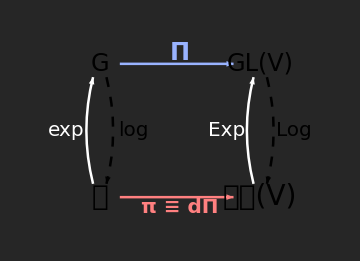

```mathematica
Graphics[{
(*Styles*)
Thickness[0.005],Arrowheads[0.04],
(*NODES*)
Text[Style["G",24,FontFamily->"Times"],{0,1}],
Text[Style["GL(V)",24,FontFamily->"Times"],{1.2,1}],
Text[Style["𝔤",28],{0,0}],
Text[Style["𝔤𝔩(V)",28],{1.2,0}],
(*HORIZONTAL ARROWS*)
(*Top Arrow: Π*)
{RGBColor[0.6,0.7,1.0],Arrow[{{0.15,1},{1.0,1}}],
Text[Style["Π",24,Bold],{0.6,1.08}]},
(*Bottom Arrow: π*)
{RGBColor[1.0,0.5,0.5],Arrow[{{0.15,0},{1.0,0}}],
Text[Style["π ≡ dΠ",20,Bold],{0.6,-0.08}]},
(*VERTICAL CURVED ARROWS (LEFT SIDE)*)
(*exp*)
{White,Arrow[BezierCurve[{{-0.05,0.1},{-0.15,0.5},{-0.05,0.9}}]],
Text[Style["exp",20,FontFamily->"Times"],{-0.25,0.5}]},
(*log*)
{Dashing[{0.02,0.02}],Arrow[BezierCurve[{{0.05,0.9},{0.15,0.5},{0.05,0.1}}]],
Text[Style["log",20,FontFamily->"Times"],{0.25,0.5}]},
(*VERTICAL CURVED ARROWS (RIGHT SIDE)*)
(*Exp*)
{White,Dashing[{}],Arrow[BezierCurve[{{1.15,0.1},{1.05,0.5},{1.15,0.9}}]],
Text[Style["Exp",20,FontFamily->"Times"],{0.95,0.5}]},
(*Log*)
{Dashing[{0.02,0.02}],Arrow[BezierCurve[{{1.25,0.9},{1.35,0.5},{1.25,0.1}}]],
Text[Style["Log",20,FontFamily->"Times"],{1.45,0.5}]}},
ImageSize->Medium,
PlotRange->{{-0.5,1.7},{-0.3,1.3}},
Background->GrayLevel[0.15]]
```

### Map the T-basis to the J-basis

#### T Basis → Matrix Rep

```mathematica
πMap[TMat_]:=
Module[{a,b,c},
{a,b,c}=ⅈ Tr[TMat.#]&/@(2 ⅈ T);
{a,b,c}.J]

(MatrixForm@*FullSimplify)/@(πMap[MatrixExp[θ #]]&/@T)
```

{(0 | 0 | 0
0 | 0 | -2 Sin[θ/2]
0 | 2 Sin[θ/2] | 0),(0 | 0 | 2 Sin[θ/2]
0 | 0 | 0
-2 Sin[θ/2] | 0 | 0),(0 | -2 Sin[θ/2] | 0
2 Sin[θ/2] | 0 | 0
0 | 0 | 0)}

#### Group Representation Map Π

```mathematica
With[{σ=PauliMatrix},
Πmap[U_]:=
Table[
1/2 Tr[σ[i].U.σ[j].U†], 
{i,3},{j,3}]];
```

```mathematica
(MatrixForm@*FullSimplify@*ComplexExpand)/@(Πmap[θ #]&/@T)
```

{(θ^2/4 | 0 | 0
0 | -θ^2/4 | 0
0 | 0 | -θ^2/4),(-θ^2/4 | 0 | 0
0 | θ^2/4 | 0
0 | 0 | -θ^2/4),(-θ^2/4 | 0 | 0
0 | -θ^2/4 | 0
0 | 0 | θ^2/4)}

```mathematica
ClearAll[commutativeDiagram];
commutativeDiagram[X_]:=
FullSimplify[
MatrixExp[πMap[X]]==
ComplexExpand[
Πmap[MatrixExp[X]]
]];
proof[And@@commutativeDiagram/@(θ T)];
```

QED■

## The Big Beautiful Example

### ℝ^3 Vector→𝔥_0 (Matrix-Vector)

```mathematica
toH0[v_List]:=Total[v*T];
fromH0[mat_]:=Table[-2 Tr[mat.T[[k]]],{k,3}];
```

### Rotation Parameters

```mathematica
Echo[vR3={x,y,z},"v_(ℝ^3) :"];
{ϕ,θ,ψ}={α,β,γ};
```

v_(ℝ^3) :  {x,y,z}

### SO(3) Rotation Matrix

#### R=R_z(ϕ).R_y(θ).R_x(ψ)=ⅇ^(ϕ J_3)ⅇ^(θ J_2)ⅇ^(ψ J_3)

```mathematica
Echo[(R=MatrixExp[ϕ J[[3]]].MatrixExp[θ J[[2]]].MatrixExp[ψ J[[1]]])//MatrixForm,"Rotation Matrix R_(ℝ^3) :"];
Echo[(vPrimeR3=Simplify[R.vR3])//MatrixForm,"v'_(ℝ^3) = R_(ℝ^3).v_(ℝ^3) :"];
```

Rotation Matrix R_(ℝ^3) :  (Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

v'_(ℝ^3) = R_(ℝ^3).v_(ℝ^3) :  (Sin[α] (-y Cos[γ]+z Sin[γ])+Cos[α] (x Cos[β]+Sin[β] (z Cos[γ]+y Sin[γ]))
Cos[α] (y Cos[γ]-z Sin[γ])+Sin[α] (x Cos[β]+Sin[β] (z Cos[γ]+y Sin[γ]))
-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ]))

### SU(2) Quaternion

#### Q_ϕθψ=ⅇ^(ϕ T_3)ⅇ^(θ T_3)ⅇ^(ψ T_3)

```mathematica
Echo[(Q=MatrixExp[ϕ T[[3]]].MatrixExp[θ T[[2]]].MatrixExp[ψ T[[1]]])//MatrixForm,"Q_ϕθψ :"];
```

Q_ϕθψ :  (ⅇ^(-(ⅈ α)/2) Cos[β/2] Cos[γ/2]+ⅈ ⅇ^(-(ⅈ α)/2) Sin[β/2] Sin[γ/2] | -ⅇ^(-(ⅈ α)/2) Cos[γ/2] Sin[β/2]-ⅈ ⅇ^(-(ⅈ α)/2) Cos[β/2] Sin[γ/2]
ⅇ^((ⅈ α)/2) Cos[γ/2] Sin[β/2]-ⅈ ⅇ^((ⅈ α)/2) Cos[β/2] Sin[γ/2] | ⅇ^((ⅈ α)/2) Cos[β/2] Cos[γ/2]-ⅈ ⅇ^((ⅈ α)/2) Sin[β/2] Sin[γ/2])

### Adjoint Action in 𝔥_0

#### v_𝔥_0=to𝔥_0(v_(ℝ^3))

```mathematica
Echo[(vH0=toH0[vR3])//MatrixForm,"v_𝔥_0 :"];
```

v_𝔥_0 :  (-(ⅈ z)/2 | -(ⅈ x)/2-y/2
-(ⅈ x)/2+y/2 | (ⅈ z)/2)

#### Q_ϕθψ v_𝔥_0(Q†)_ϕθψ

```mathematica
Echo[(vPrimeH0=Simplify[ComplexExpand[Q.vH0.Q†]])//MatrixForm,"v'_𝔥_0=Q :"];
```

v'_𝔥_0=Q :  (-1/2 ⅈ (-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ])) | -1/2 ⅈ (Cos[α]-ⅈ Sin[α]) (x Cos[β]+Cos[γ] (-ⅈ y+z Sin[β])+(ⅈ z+y Sin[β]) Sin[γ])
1/2 (-ⅈ Cos[α]+Sin[α]) (x Cos[β]+Cos[γ] (ⅈ y+z Sin[β])+(-ⅈ z+y Sin[β]) Sin[γ]) | 1/2 ⅈ (-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ])))

### Proofs

#### Proof 1: Consistency of the Pauli Map

```mathematica
Echo[proof[Simplify[
fromH0[toH0[vR3]]==vR3
]],"Pauli Map Round Trip: ℝ^3 → 𝔥_0 → ℝ^3 :"];
```

QED■

Pauli Map Round Trip: ℝ^3 → 𝔥_0 → ℝ^3 :  True

#### Proof 2: SO(3) from SU(2)

Matrix elements of R_ϕθψ are R_ij=-2 Tr(T_j Q_ϕθψ T_j(Q†)_ϕθψ)

```mathematica
Echo[(RFromQ=Table[
-2Tr[T[[i]].Q.T[[j]].Q†]//
ComplexExpand//Simplify,
{i,3},{j,3}])//MatrixForm,"R_ij=-2Tr[T_i·Q·T_j·Q†] :"];
proof[RFromQ==R];
```

R_ij=-2Tr[T_i·Q·T_j·Q†] :  (Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

QED■

### Proof 3: Equivalence of the Rotated Vectors

Does the SU(2) rotated v'_𝔥_0 mat-vec map back to the SO(3) rotated vector v'_(ℝ^3)?

```mathematica
proof[Simplify[
fromH0[vPrimeH0]==vPrimeR3
]];
```

QED■